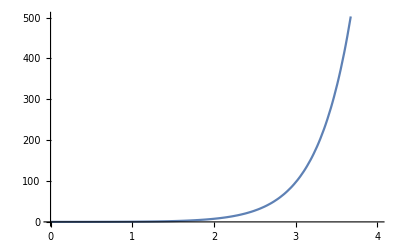

```mathematica
Plot[(9^n-8^n)/Sqrt[5],{n,0,4}]
```

```mathematica
f[x_,fr_]:=Exp[-2*Pi*I*fr*x]; (*Fourier Transfromation, general equation*)
g[t_] := (9^t-8^t)/Sqrt[5]; (*The function being transformed *)
Manipulate[ParametricPlot[{Re[g[t]*f[t,fr]],Im[g[t]*f[t,fr]]},{t,0,4},PlotRange->{-60,60}],{fr,0,3,0.1}]
```

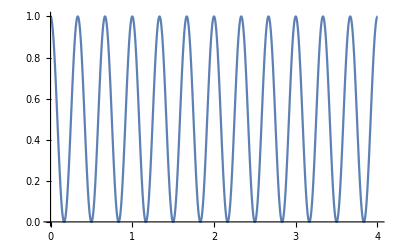

```mathematica
h[t_]:=1/2(1+Sin[6 Pi t + Pi/2])
Plot[h[t],{t,0,4}]
```

```mathematica
ParametricPlot[{fr,Re[Integrate[(h[t]*f[t,fr]),{t,0,4}]]},{fr,0,5}, PlotRange->{{0,5},{-2,2}}]
```